exp (ı θ+Ω^*)+C'==0

```mathematica
SubOm = Ω-> I θ  + Log[Conjugate[-CC']]
```

Ω→ⅈ θ+Log[-Conjugate[CC']]

```mathematica
Eq = κ Ω' - 2 Exp[I θ] (p + Exp[- 2 I θ] CC'/Conjugate[CC'])
```

-2 ⅇ^(ⅈ θ) (p+(ⅇ^(-2 ⅈ θ) CC')/Conjugate[CC'])+κ Ω'

```mathematica
EqC = Simplify[Conjugate[CC']Eq/.{Ω' -> I + CC''/Conjugate[CC']}]
```

(-2 ⅇ^(ⅈ θ) p+ⅈ κ) Conjugate[CC']-2 ⅇ^(-ⅈ θ) CC'+κ CC''

```mathematica
Sub = {CC' -> XP + I YP,CC'' -> XP' + I YP'};
```

```mathematica
Eq1 = EqC/.Sub
```

-2 ⅇ^(-ⅈ θ) (XP+ⅈ YP)+(-2 ⅇ^(ⅈ θ) p+ⅈ κ) (Conjugate[XP]-ⅈ Conjugate[YP])+κ (XP'+ⅈ YP')

```mathematica
Eq2 =ExpToTrig[FullSimplify[Eq1,{p,κ,θ, XP, YP, XP', YP'}ϵReals]]
```

ⅈ κ Conjugate[XP]+κ Conjugate[YP]-2 XP Cos[θ]-2 ⅈ YP Cos[θ]-2 p Conjugate[XP] Cos[θ]+2 ⅈ p Conjugate[YP] Cos[θ]+2 ⅈ XP Sin[θ]-2 YP Sin[θ]-2 ⅈ p Conjugate[XP] Sin[θ]-2 p Conjugate[YP] Sin[θ]+κ XP'+ⅈ κ YP'

```mathematica
Eq3=ComplexExpand[ReIm[Eq2]]
```

{YP κ-2 XP Cos[θ]-2 p XP Cos[θ]-2 YP Sin[θ]-2 p YP Sin[θ]+κ XP',XP κ-2 YP Cos[θ]+2 p YP Cos[θ]+2 XP Sin[θ]-2 p XP Sin[θ]+κ YP'}

```mathematica
Sol3=FullSimplify[Solve[ #==0& /@Eq3,{XP',YP'}][[1]]]
```

{XP'→(-YP κ+2 (1+p) XP Cos[θ]+2 (1+p) YP Sin[θ])/κ,YP'→-(2 (-1+p) YP Cos[θ]+XP (κ-2 (-1+p) Sin[θ]))/κ}

```mathematica
Sol3
```

{XP'→(-YP κ+2 (1+p) XP Cos[θ]+2 (1+p) YP Sin[θ])/κ,YP'→-(2 (-1+p) YP Cos[θ]+XP (κ-2 (-1+p) Sin[θ]))/κ}

```mathematica
AllSub = #->#[θ]& /@{XP,YP}
```

{XP→XP[θ],YP→YP[θ]}

```mathematica
XPP = ({XP', YP'}/.Sol3)/.AllSub
```

{(2 (1+p) Cos[θ] XP[θ]-κ YP[θ]+2 (1+p) Sin[θ] YP[θ])/κ,-((κ-2 (-1+p) Sin[θ]) XP[θ]+2 (-1+p) Cos[θ] YP[θ])/κ}

```mathematica
EqXY = {XP'[θ] ==XPP[[1]], YP'[θ] == XPP[[2]]}
```

{XP'[θ]==(2 (1+p) Cos[θ] XP[θ]-κ YP[θ]+2 (1+p) Sin[θ] YP[θ])/κ,YP'[θ]==-((κ-2 (-1+p) Sin[θ]) XP[θ]+2 (-1+p) Cos[θ] YP[θ])/κ}

```mathematica
DSolve[EqXY,{XP, YP}, θ]
```

DSolve[{XP'[θ]==(2 (1+p) Cos[θ] XP[θ]-κ YP[θ]+2 (1+p) Sin[θ] YP[θ])/κ,YP'[θ]==-((κ-2 (-1+p) Sin[θ]) XP[θ]+2 (-1+p) Cos[θ] YP[θ])/κ},{XP,YP},θ]

```mathematica
Alpha[θ_] := Min[Abs[θ], Pi - Abs[θ]];
Curve[X_, Y_, α_] := {Sign[Cos[α]]X[Alpha[α]],Sign[Sin[α]]Y[Alpha[α]]};
```

```mathematica
Sol1[p_] :=Check[
Module[{sol, ϵ= 10^(-16)},
sol=
TimeConstrained[
NDSolve[
Join[
With[{κ = Z[θ]^2 + ϵ},
{XP'[θ]==(2 (1+p) Cos[θ] XP[θ]-κ YP[θ]+2 (1+p) Sin[θ] YP[θ])/κ,
YP'[θ]==-((κ-2 (-1+p) Sin[θ]) XP[θ]+2 (-1+p) Cos[θ] YP[θ])/κ}], 
{
X'[θ] ==XP[θ],
Y'[θ] == YP[θ]
},
{Z'[θ] ==0},
{
XP[0] ==0,
Y[0] ==0,
X[Pi/2] ==0,
Y[Pi/2]==1,
YP[Pi/2]==0
}
], {XP,YP,X,Y, Z},{θ,0,Pi/2},WorkingPrecision->MachinePrecision,Method->"Adams"][[1]]
,60*60];
{X, Y,XP,YP,Z[0]^2 + ϵ}/.sol
],
{Null,Null,Null,Null, Null}
]
```

```mathematica
Sol1[-0.01]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],0.774312}

```mathematica
Plt1[p0_] :=
Module[{X0,Y0,XP0, YP0, κ0},
{X0,Y0,XP0,YP0, κ0}= Sol1[p0];
Print["p = ",p0, ", κ= ",κ0];
XY =Plot[ {X0[α],Y0[α]},{α,0,Pi/2},PlotLegends->Placed[{X,Y},Above],PlotRange->All];
P1 =ParametricPlot[Curve[X0,Y0,α],{α,-Pi,Pi},PlotRange->All];
Grid[{
{TraditionalForm[{p==p0,κ==κ0}],SpanFromLeft},
{Show[XY,ImageSize->{600,400},AspectRatio->Full],Show[P1,PlotRange->All,ImageSize->{240,400},AspectRatio->Full]}
}]
];
```

p = -0.5, κ= 0.469132

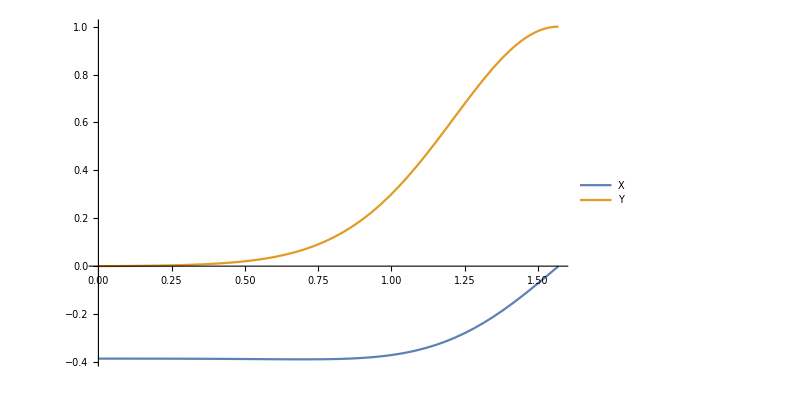
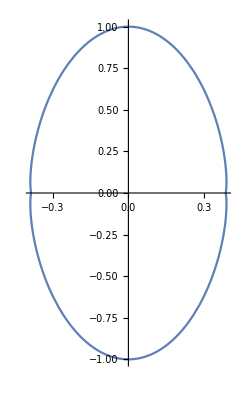
{p==-0.5,κ==0.469132} | 
-Graphics- | -Graphics-

```mathematica
Plt1[-0.5]
```

```mathematica
Tubes[p1_, p2_] :=
Module[{X1,Y1,XP1,YP1,X2, Y2,XP2,YP2, κ1, κ2, P1, P2},
{X1,Y1,XP1,YP1, κ1}= Sol1[p1];
{X2,Y2,XP2,YP2, κ2}= Sol1[p2];
P1 =ParametricPlot[Curve[X1,Y1,α],{α,-Pi,Pi},PlotRange->All, PlotLabel->p ==p1];
P2 =ParametricPlot[Curve[X2,Y2,α],{α,-Pi,Pi},PlotRange->All, PlotLabel->p ==p2];
Grid[{
{Show[P1,PlotRange->All,ImageSize->{240,400},AspectRatio->Full],Show[P2,PlotRange->All,ImageSize->{240,400},AspectRatio->Full]}
}]
];
```

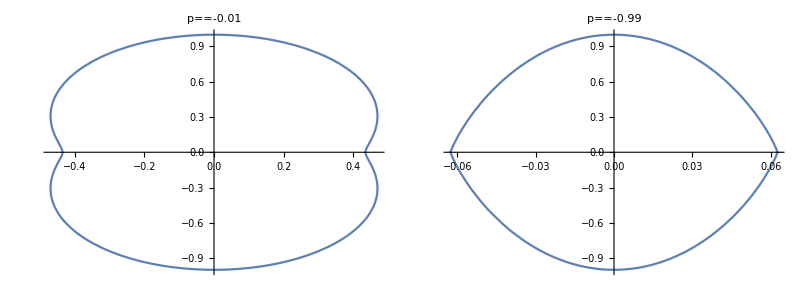

f'==exp q κ Ω==-exp ı q θ κ F^*

```mathematica
Tubes[-0.01,-0.99]
```

```mathematica
GammaSol1[p_,q_] := Module[{X,Y,Xp, Yp, gsol, κ},
{X,Y,Xp, Yp,κ} = Sol1[p/q];
gsol = 
NDSolve[
{G'[θ] == -κ q Cos[θ] (Xp[θ]^2 + Yp[θ]^2),
G[0] ==0},G,{θ,0,Pi/2},WorkingPrecision->MachinePrecision,Method->"Adams"][[1]];
{G/.gsol,κ}
];
```

```mathematica
GammaPlot1[p_,q_] := 
Module[{G,κ},
{G,κ} = GammaSol1[p,q];
Print["κ== ",κ, ": Delta Gamma[Pi]= ", 2 G[Alpha[Pi]]]; 
Plot[Sign[θ]G[Alpha[θ]],{θ,-Pi,Pi},PlotRange->All, PlotLabel->{Γ: "p==",p" q==",q" κ==",κ},ImageSize->{Medium,Small},AspectRatio->Full]
];
```

κ== 0.645909: Delta Gamma[Pi]= 0.

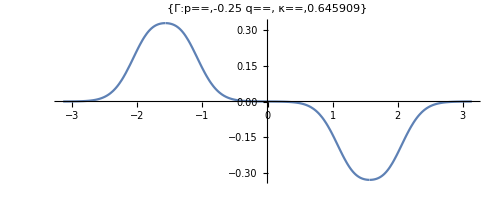

```mathematica
GammaPlot1[-0.25,1]
```

```mathematica
Gammas[p1_, p2_] :=
Module[{ P1, P2},
P1 =GammaPlot1[p1,1];
P2 =GammaPlot1[p2,1];
Grid[{
{Show[P1,PlotRange->All,ImageSize->{240,400},AspectRatio->Full],Show[P2,PlotRange->All,ImageSize->{240,400},AspectRatio->Full]}
}]
];
```

κ== 0.774312: Delta Gamma[Pi]= 0.

κ== 0.00999985: Delta Gamma[Pi]= 0.

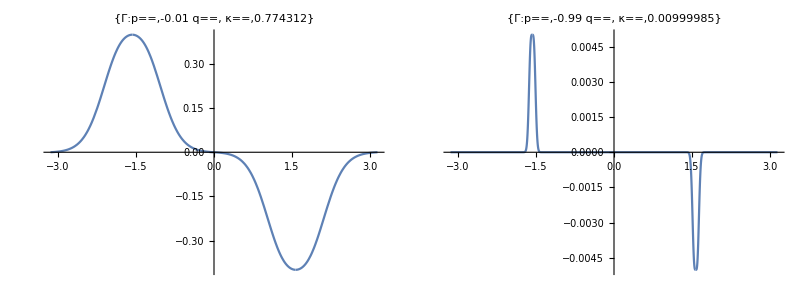

```mathematica
Gammas[-0.01,-0.99]
```

```mathematica
(* Energy *)
Coulomb[η_, L_]:= Assuming[{L>0, η>0},Integrate[1/( 8 Pi Sqrt[z^2 +η^2]),{z,-L,L}] ]
```

```mathematica
LimitCoulomb[η_] =Assuming[{ η>0},Limit[Coulomb[η, L] -Log[2L]/(4 Pi), L ->+Infinity]]
```

-Log[η]/(4 π)

```mathematica
(* 
NIntegrate[
 Cos[θ2]
(Xs'[θ2]^2 + Ys'[θ2]^2)^2(Xs[θ2]^2  + Ys[θ2]^2)^2
(Log[(X1-Xs[θ2])^2  + (Y1-Ys[θ2])^2 + ϵ] +
Log[(X1-Xs[θ2])^2  + (Y1+Ys[θ2])^2 + ϵ]),
{θ2,0,θ1}
] 
*)
SecondIntegral[X_, Y_,Xp_, Yp_,  θ1_] :=
Module [
{ϵ=10^(-8), X1, Y1 },
{X1,Y1} = Curve[X,Y,θ1];
NIntegrate[
Block[{X2,Y2, α},
{X2,Y2} = Curve[X,Y,θ];
α = Alpha[θ];
Cos[θ] (Xp[α]^2  + Yp[α]^2)^2
Log[(X1-X2)^2  + (Y1-Y2)^2 + ϵ]],
{θ,0,θ1},Method->"GaussKronrodRule"
]
];
```

```mathematica
InterpInt[X_, Y_,Xp_, Yp_, M_] :=
Module[{tbl},
tbl = Table[SecondIntegral[X, Y,Xp, Yp,  θ],{θ,0,Pi,Pi/M}];
Interpolation[tbl,{{0,Pi}}]
];
```

```mathematica
Energy[p_,M_:32] :=
Module[{X,Y,Xp,Yp, κs,SI, ϵ= 10^(-8)},
{X,Y,Xp,Yp, κs} = Sol1[p];
If[NumberQ[κs] &&κs∈Reals,
SI = InterpInt[X, Y,Xp, Yp,M];
{p,
-κs^2/Pi
NIntegrate[
 SI[θ] Cos[θ](Xp[Alpha[θ]]^2  + Yp[Alpha[θ]]^2)^2,{θ,0,Pi},
Method->"GaussKronrodRule"
]}
,
{p, Missing[]}
]
];
```

```mathematica
interpE = Module[{data},
data = Table[Energy[p,64],{p,-0.99,-0.01,0.01}];
Interpolation[DeleteCases[data,{_,Missing[]}],InterpolationOrder->2]
];

Plot[interpE[p],{p,-1,0},PlotLabel->"Energy vs p/q"]
(*2 ⅇ^(-(ζ+3 r^2 ζ)/PP[r]) √(3/π) (1-9 r^2) ζ^(3/2) (1/PP[r])^(5/2)*)
PE[ζ_] := 2 Sqrt[3/Pi]
NIntegrate[ζ^(3/2) Abs[1-9 r^2]/interpE[r]^(5/2) Exp[-(3 r^2+1) (ζ/interpE[r])],{r,-0.999,-0.001},Method->"GaussKronrodRule"];
LogLogPlot[PE[ζ],{ζ,0.0001,10},PlotLabel->"Energy PDF"]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point θ == 4.07139×10^-14.

NDSolve::berr: The scaled boundary value residual error of 1.01322 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

$Aborted

```mathematica
F[p_] :=
Module[{X,Y,Xp,Yp,κ},
{X,Y,Xp,Yp,κ} = Sol1[p];
If[NumberQ[κ] &&κ∈Reals,
{p,Sqrt[-p/Pi] κ^2 NIntegrate[Cos[θ]^2 ( Xp[Alpha[θ]]^2 + Yp[Alpha[θ]]^2)^(5/2),{θ,0,Pi},Method->"Trapezoidal",PrecisionGoal->6]}
,{p,Missing[]}
]
];
```

```mathematica
F[-0.25]
```

{-0.25,0.093673}

```mathematica
F[-1]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point θ == 4.23261×10^-14.

NDSolve::berr: The scaled boundary value residual error of 1.06986 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{-1,Missing[]}

```mathematica
{Sol1[-1+0.1],Sol1[-1+0.2]}
```

{{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],0.0998338},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],0.198507}}

```mathematica
ClearAll[zz];
```

```mathematica
Sol1[-0.5]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],0.469132}

```mathematica
Table[-1+v^2,{v,0.5,0.8,0.1}]
```

{-0.75,-0.64,-0.51,-0.36}

```mathematica
Table[Sol1[-1+v^2],{v,0.5,0.8,0.1}]
```

{{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],0.246908},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],0.349573},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],0.461073},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],0.573879}}

```mathematica
data = ParallelTable[F[v],{v ,-1,0,0.01}];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point θ == 
              -14
    4.23261 10   .

NDSolve::berr: The scaled boundary value residual error of 1.06986
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::mxst: Maximum number of 10000 steps reached at the point θ == 
              -14
    4.10013 10   .

NDSolve::berr: The scaled boundary value residual error of 1.22642
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::mxst: Maximum number of 10000 steps reached at the point θ == 
              -14
    4.07139 10   .

NDSolve::berr: The scaled boundary value residual error of 1.01322
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

```mathematica
Finterp = Interpolation[Select[data,NumericQ[#[[2]]]&],InterpolationOrder->2];
```

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

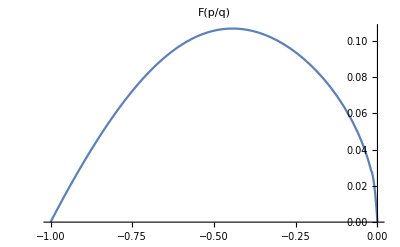

```mathematica
Plot[Finterp[p],{p,-1,0}, PlotLabel->"F(p/q)",PlotRange->All]
```

```mathematica
PP[ζ_] := 
NIntegrate[3 ζ Abs[1-9 r^2]/(5 Finterp[r]^2) Exp[-(3 r^2+1) (ζ/Finterp[r])^(4/5)],{r,-0.999,-0.001},Method->"GaussKronrodRule"]
```

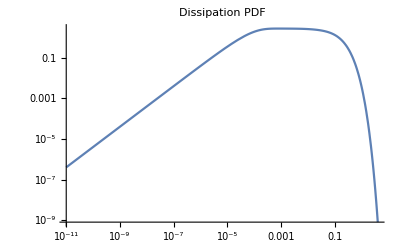

```mathematica
LogLogPlot[PP[ζ],{ζ,0.00000000001,4},PlotLabel->"Dissipation PDF"]
```

```mathematica
Surf[X_,Y_,R0_,z_,θ_,ρ_]:= Module[{ξ, CC},
CC=R0 Curve[X,Y,θ];
ξ=E^(I ρ)(CC[[1]] + I CC[[2]]);
Join[ReIm[ξ],{z}]
];
```

```mathematica
ClearAll[Noodle,MakeSols];
MakeSols[p1_,p2_]:=Module[{X1,Y1,X2,Y2},
{X1,Y1} = Sol1[p1][[;;2]];
{X2,Y2} = Sol1[p2][[;;2]];
{X1,Y1,X2,Y2}
];
Noodle[{X1_,Y1_,X2_,Y2_}, l_,  λ_] :=
Module[{R0,T0},
ParametricPlot3D[
Module[{
z1 =Sin[ω1 t], 
z2 = Sin[ω2 t]
},
(1-t)Surf[X1,Y1,t,t l,θ,λ t]+t Surf[X2,Y2,t,t l,θ,λ t]
],{θ,-Pi,Pi},{t,0,1}, Mesh->None, Boxed->False, Axes->False,MaxRecursion->8,PlotRange->All]
];
```

```mathematica
sols=MakeSols[-0.99,-0.01];
```

```mathematica
Noodle[sols, 5, Pi/2]
```

-Graphics3D-

```mathematica
(* Mean Field Theory*)
```

```mathematica
PSquared[p_] :=  Module[{Xs,Ys,Xps,Yps,κs},
{Xs,Ys,Xps,Yps,κs} = Sol1[p];
If[NumberQ[κs] &&κs∈Reals,
 {p,(6κs NIntegrate[Cos[θ]Xs[θ](Xps[θ]^2 +Yps[θ]^2),{θ,0,Pi/2},Method->"GaussKronrodRule"])^2}
,
{p,Missing[]}
]
];
```

```mathematica
PSquared[-0.5]
```

{-0.5,0.210723}

```mathematica
data = ParallelTable[PSquared[p],{p,-1,0,0.01}];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point θ == 
              -14
    4.23261 10   .

NDSolve::mxst: Maximum number of 10000 steps reached at the point θ == 
              -14
    4.10013 10   .

NDSolve::berr: The scaled boundary value residual error of 1.06986
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 1.22642
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::mxst: Maximum number of 10000 steps reached at the point θ == 
              -14
    4.07139 10   .

NDSolve::berr: The scaled boundary value residual error of 1.01322
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

```mathematica
interpPsqr= Interpolation[DeleteCases[data,{_,Missing[]}],InterpolationOrder->2];
```

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

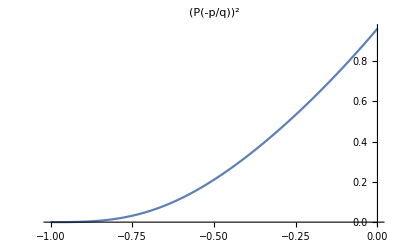

```mathematica
Plot[interpPsqr[x],{x,-1,0},PlotLabel->P[-p/q]^2]
```

```mathematica
interpPsqr[-1/2]
```

0.210723

```mathematica
MeanPsqr[iii_] :=
Module[{},
15 Sqrt[3]/4
(
NIntegrate[(
1-9 r^2) iii[r]/(1 + 3 r^2)^(7/2),{r,-1/3,0},Method->"GaussKronrodRule"] +
NIntegrate[(-1+9 r^2) iii[r]/(1 + 3 r^2)^(7/2),{r,-1,-1/3},Method->"GaussKronrodRule"]
)];
```

```mathematica
MeanPsqr[interpPsqr]
```

0.977281

```mathematica
5589/(32 Pi^2) MeanPsqr[interpPsqr]
```

17.2943

```mathematica
17.29433496034603^(-1/6)
```

0.621846

```mathematica
0.6218457764460924^(-2/5)
```

1.20928

```mathematica
Dissipation[iii_] := NIntegrate[(2 √(3/π) Abs[1-9 r^2] Gamma[15/4])/((1+3 r^2)^(15/4))iii[r],{r,-1,0},Method->"GaussKronrodRule"];
```

```mathematica
Dissipation[interpPsqr]
```

0.171446

```mathematica
0.1714457321782006^(-2/5)
```

2.02465